# Triangular Automata Package Demonstration

This notebook demonstrates how to use the functions of the Triangular Automata package to compute and display cellular automata in an infinite triangular grid.

Paul Cousin
https://orcid.org/0000-0002-3866-7615

## Introduction

Triangular Automata is a short name for cellular automata in a triangular grid. With this package, you will be able to play with them in a simple and efficient way. More details and informations can be found at: https://paulcousin.github.io/triangular-automata

First, let’s import the package:

```mathematica
<<(NotebookDirectory[]<>"TriangularAutomata.wl");
```

## Rules

In this package, only a subset of possible Triangular Automata is considered. Here are the restrictions:

binary states: s∈{0≡"dead"≡GrayLevel[1], 1≡"alive"≡RGBColor[0.5, 0, 0.5]}

only the first neighborhood is taken into account

orientation of the neighbors is not considered

This means that there are only 8 possible local configurations that can be plotted with TAConfigurationPlot.

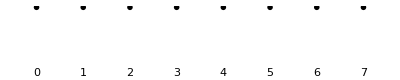

```mathematica
GraphicsGrid@{Table[TAConfigurationPlot[n],{n,0,7,1}],Range[0,7]}
```

A rule must the specify for every configuration, if the cell is going to be dead or alive at  t+1. There are thus only 2^8=256 rules which map a configuration to as future state. These rules can for indexed by a unique rule number n in the Wolfram Code style.

```mathematica
n=∑_(c=0)^7 2^c R[c]
```

Rule can be plotted with the TARulePlot function.

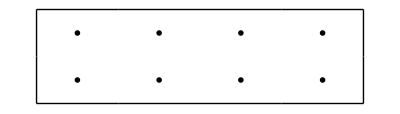
181  =  10110101_2
-Graphics-

```mathematica
TARulePlot[181, "Labeled"->True]
```

The “Labeled” option  adds the rule number in base 10 and in base 2 as a title. We see that the behavior of the rule is capture in its binary digits. Starting from the right, they indicate the future state for each configuration as they have been ordered previously.

## Starting Points

Grids have a special format. They are captured in a list with three elements: an adjacency matrix, a state vector and a coordinates vector. The first two are in the SparseArray format.

To simplify things, this package provides few starting points ready to use:

TAStartOneAlive: a grid with only one alive cell at the center

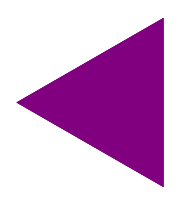

```mathematica
TAGridPlot@TAStartOneAlive
```

TAStartLogo: a grid with a logo that contains all 8 local configurations.

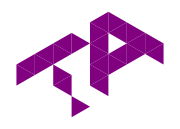

```mathematica
TAGridPlot@TAStartLogo
```

TAStartRandom[n]: a grid with cells randomly alive or dead on n layers.

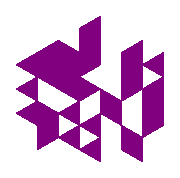

```mathematica
TAGridPlot@TAStartRandom[6]
```

## Evolution

We can now evolve these grids with different rules. The most simple function to do so is TAEvolve. Let’s use it to evolve TAStartOneAlive with rule 181.

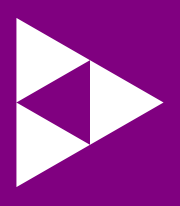

```mathematica
TAGridPlot@TAEvolve[TAStartOneAlive, 181]
```

As expected from the earlier plot of rule 181, the environment has become alive and we have three dead cell surrounding a central alive cell. It would be nice to see what will happen after that. The function TANestEvolve can be used to jump ahead several time steps. Let’s look at what TAStartOneAlive will look like 64 time steps later when evolved by rule 181, with TANestEvolve.

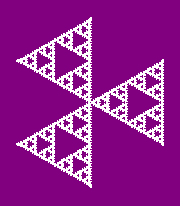

```mathematica
TAGridPlot@TANestEvolve[TAStartOneAlive, 181,64]
```

With this function, all the intermediate steps are lost and we only get the last grid. TANestListEvolve returns a list with all the intermediate steps.

```mathematica
GraphicsGrid@ArrayReshape[TAGridPlot[#]&/@TANestListEvolve[TAStartOneAlive, 181,64],{8,8}]
```

-Graphics-

TAEvolutionPlot shows an animated version of what we have just computed.

```mathematica
TAEvolutionPlot[TAStartOneAlive,181,64]
```

Like with Wolfram’s elementary automata, the grid evolution can be plotted all at once in 3D with TAEvolutionPlot3D. You can rotate this plot to look at it from different angles.

```mathematica
TAEvolutionPlot3D[TAStartOneAlive,181,64]
```

-Graphics3D-

## Conclusion

I hope you will enjoy this package. Share what interesting things you find with it!